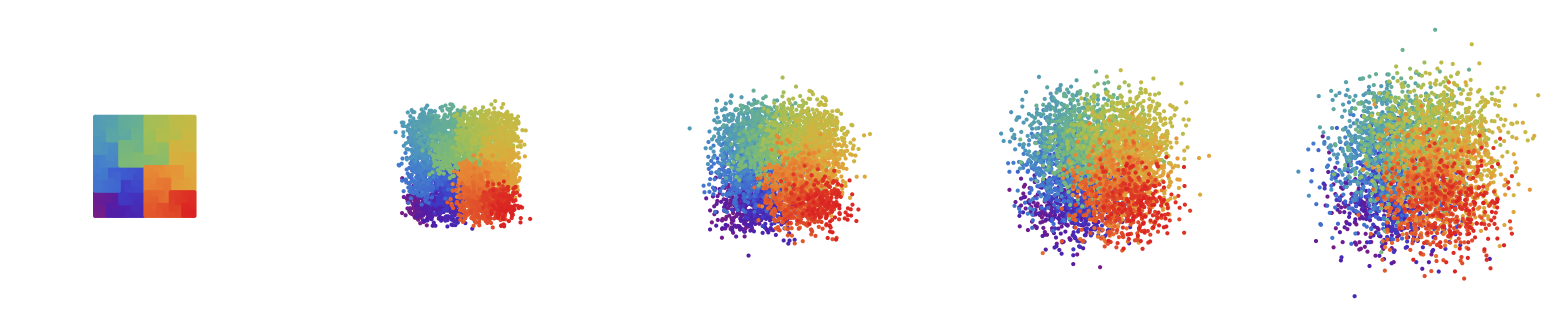

```mathematica
(*Panel A: small 2D Hilbert for panel A*)
q=0;data2d=First@HilbertCurve[6];length=Length@data2d-1;
tmplist[0]=data2d;
tmplist[4]=(#+RandomReal[NormalDistribution[0,4],2])&/@data2d;
tmplist[8]=(#+RandomReal[NormalDistribution[0,8],2])&/@data2d;
tmplist[12]=(#+RandomReal[NormalDistribution[0,12],2])&/@data2d;
tmplist[16]=(#+RandomReal[NormalDistribution[0,16],2])&/@data2d;
With[{all=Flatten[Join[Table[tmplist[i],{i,0,16,4}]],1]},GraphicsRow[Table[Show[Graphics[{ColorData["Rainbow"][#/(length+1)],Point[tmplist[i][[#]]]}&/@Range[1,length+1]],PlotRange->{{Min@all[[All,1]],Max@all[[All,1]]},{Min@all[[All,2]],Max@all[[All,2]]}}],{i,0,16,4}]]]
```

```mathematica
(*2D Hilbert curve diffusion*)
order=10;
data2d=First@HilbertCurve[order];(*define another 2D curve here*)
length=Length@data2d-1;
For[q=0,q<=16,
{
Print@q;
iter=0;
keeplist[q]={};
While[iter<1,(*change, e.g. to 10 to average across 10 diffusion experiments*)
{
If[q==0,diffdata=data2d,
diffdata=(#+RandomReal[NormalDistribution[0,q],2])&/@data2d];
list=DeleteDuplicates@Sort@Flatten[Join[Cases[If[Length@#>1,Subsets[#[[All,3]],{2}]]&/@GatherBy[Table[{Floor[(diffdata[[i,1]]-1)/2],Floor[(diffdata[[i,2]]-1)/2],i},{i,1,length+1}],#[[1]]&&#[[2]]&],Except[Null]],
Cases[If[Length@#>1,Subsets[#[[All,3]],{2}]]&/@GatherBy[Table[{Floor[(diffdata[[i,1]]-1)/2],Floor[(diffdata[[i,2]])/2],i},{i,1,length+1}],#[[1]]&&#[[2]]&],Except[Null]],
Cases[If[Length@#>1,Subsets[#[[All,3]],{2}]]&/@GatherBy[Table[{Floor[(diffdata[[i,1]])/2],Floor[(diffdata[[i,2]]-1)/2],i},{i,1,length+1}],#[[1]]&&#[[2]]&],Except[Null]],
Cases[If[Length@#>1,Subsets[#[[All,3]],{2}]]&/@GatherBy[Table[{Floor[(diffdata[[i,1]])/2],Floor[(diffdata[[i,2]])/2],i},{i,1,length+1}],#[[1]]&&#[[2]]&],Except[Null]]
],1];
AppendTo[keeplist[q],list];
};iter++];
keeplist[q]=Flatten[keeplist[q],1];
};q+=4]
```

0

4

8

12

16

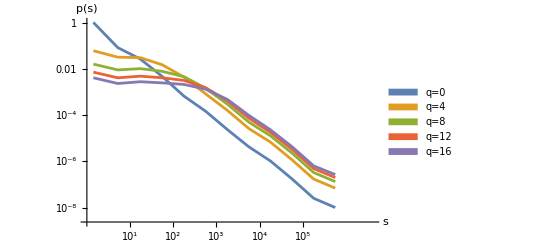

```mathematica
(*Log-Log contact probability curves*)
lowbound=1;highbound=length;step=.5;dim=2;
Show[ListLogPlot[Table[With[{tab=BinCounts[N@Log[10,Abs[#[[2]]-#[[1]]]]&/@keeplist[q],{N@Log[10,lowbound],N@Log[10,highbound],step}]},Table[With[{a=IntegerPart[10^(Log[10,lowbound]+(i-1)step)],b=IntegerPart[10^(Log[10,lowbound]+i step)-1]},{(Log[10,a]+Log[10,b])/2,1/iter *tab[[i]]/((length-a+length-b)/2*(b-a+1))}],{i,1,Length@tab}]],{q,0,16,4}],PlotRange->{{Log[10,lowbound],1.1*Log[10,highbound]},Full},Joined->True,PlotLegends->SwatchLegend["q="~~ToString[#]&/@Range[0,16,4]]],AxesLabel->{"s","p(s)"},AxesStyle->Directive[Black],Ticks->{Table[{i,Superscript[10,i]},{i,1,5}],{Log[#],NumberForm[N@#]}&/@{10^-6,0.001,1}},LabelStyle->Directive[Larger,Black]]
```

```mathematica
(*3D Hilbert curve diffusion*)
order=7;
data3d=First@HilbertCurve[order,3];(*define another 3D curve here*)
length=Length@data3d-1;
For[q=0,q<=16,
{
Print@q;
iter=0;
keeplist[q]={};
While[iter<1,
{
diffdata=(#+RandomReal[NormalDistribution[0,q],3])&/@data3d;
list=DeleteDuplicates@Sort@Flatten[Join[
Cases[If[Length@#>1,Subsets[#[[All,1]],{2}]]&/@GatherBy[
Table[{i,
Floor[(diffdata[[i,1]]-1)/2],
Floor[(diffdata[[i,2]]-1)/2],
Floor[(diffdata[[i,3]]-1)/2]},{i,1,length+1}],#[[2]]&&#[[3]]&&#[[4]]&],Except[Null]],
Cases[If[Length@#>1,Subsets[#[[All,1]],{2}]]&/@GatherBy[
Table[{i,
Floor[(diffdata[[i,1]]-1)/2],
Floor[(diffdata[[i,2]]-1)/2],
Floor[(diffdata[[i,3]])/2]},{i,1,length+1}],#[[2]]&&#[[3]]&&#[[4]]&],Except[Null]],
Cases[If[Length@#>1,Subsets[#[[All,1]],{2}]]&/@GatherBy[
Table[{i,
Floor[(diffdata[[i,1]]-1)/2],
Floor[(diffdata[[i,2]])/2],
Floor[(diffdata[[i,3]])/2]},{i,1,length+1}],#[[2]]&&#[[3]]&&#[[4]]&],Except[Null]],
Cases[If[Length@#>1,Subsets[#[[All,1]],{2}]]&/@GatherBy[
Table[{i,
Floor[(diffdata[[i,1]]-1)/2],
Floor[(diffdata[[i,2]])/2],
Floor[(diffdata[[i,3]]-1)/2]},{i,1,length+1}],#[[2]]&&#[[3]]&&#[[4]]&],Except[Null]],
Cases[If[Length@#>1,Subsets[#[[All,1]],{2}]]&/@GatherBy[
Table[{i,
Floor[(diffdata[[i,1]])/2],
Floor[(diffdata[[i,2]]-1)/2],
Floor[(diffdata[[i,3]]-1)/2]},{i,1,length+1}],#[[2]]&&#[[3]]&&#[[4]]&],Except[Null]],
Cases[If[Length@#>1,Subsets[#[[All,1]],{2}]]&/@GatherBy[
Table[{i,
Floor[(diffdata[[i,1]])/2],
Floor[(diffdata[[i,2]]-1)/2],
Floor[(diffdata[[i,3]])/2]},{i,1,length+1}],#[[2]]&&#[[3]]&&#[[4]]&],Except[Null]],
Cases[If[Length@#>1,Subsets[#[[All,1]],{2}]]&/@GatherBy[
Table[{i,
Floor[(diffdata[[i,1]])/2],
Floor[(diffdata[[i,2]])/2],
Floor[(diffdata[[i,3]])/2]},{i,1,length+1}],#[[2]]&&#[[3]]&&#[[4]]&],Except[Null]],
Cases[If[Length@#>1,Subsets[#[[All,1]],{2}]]&/@GatherBy[
Table[{i,
Floor[(diffdata[[i,1]])/2],
Floor[(diffdata[[i,2]])/2],
Floor[(diffdata[[i,3]]-1)/2]},{i,1,length+1}],#[[2]]&&#[[3]]&&#[[4]]&],Except[Null]]
],1];

AppendTo[keeplist[q],list];
};iter++];
keeplist[q]=Flatten[keeplist[q],1];
};q+=4]
```

0

4

8

12

16

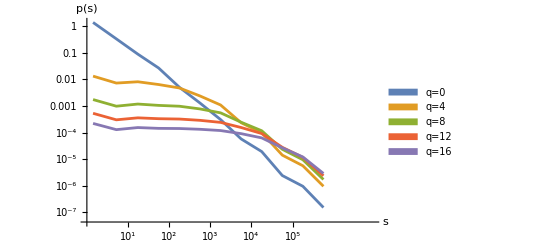

```mathematica
(*log-log contact probability curves*)
lowbound=1;highbound=length;step=.5;
Show[ListLogPlot[Table[With[{tab=BinCounts[N@Log[10,Abs[#[[2]]-#[[1]]]]&/@keeplist[q],{N@Log[10,lowbound],N@Log[10,highbound],step}]},Table[
With[{
a=IntegerPart[10^(Log[10,lowbound]+(i-1)step)],b=IntegerPart[10^(Log[10,lowbound]+i step)-1]},{(Log[10,a]+Log[10,b])/2,1/iter *tab[[i]]/((length-a+length-b)/2*(b-a+1))}],{i,1,Length@tab}]],{q,0,16,4}],PlotRange->{{Log[10,lowbound],1.1*Log[10,highbound]},Full},Joined->True(*,InterpolationOrder->2*),PlotLegends->SwatchLegend["q="~~ToString[#]&/@Range[0,16,4]]],AxesLabel->{"s","p(s)"},AxesStyle->Directive[Black],Ticks->{Table[{i,Superscript[10,i]},{i,1,5}],{Log[#],NumberForm[N@#]}&/@{10^-6,0.001,1}},LabelStyle->Directive[Larger,Black]]
```

```mathematica
(*Other random stuff to be deleted*)
```

```mathematica
For[q=4,q<=16,{
tab=BinCounts[N@Log[10,Abs[#[[2]]-#[[1]]]]&/@keeplist[q],{N@Log[10,lowbound],N@Log[10,highbound],step}];
newtab=Table[With[{a=IntegerPart[10^(Log[10,lowbound]+(i-1)step)],b=IntegerPart[10^(Log[10,lowbound]+i step)-1]},{(Log[10,a]+Log[10,b])/2,Log[10,1/iter *tab[[i]]/((length-a+length-b)/2*(b-a+1))]}],{i,1,Length@tab}];
res[q]=x/.First@Solve[Fit[newtab[[2;;4]],{1},x]==Fit[newtab[[-4;;-2]],{1,x},x]]
};q+=4];
Fit[Table[{Log[10,q],res[q]},{q,4,16,4}],{1,x},x];
ListPlot[Table[{Log[10,q],res[q]},{q,4,16,4}]]
```

```mathematica
q=8;Fit[N@With[{tab=BinCounts[N@Log[10,Abs[#[[2]]-#[[1]]]]&/@keeplist[q],{N@Log[10,lowbound],N@Log[10,highbound],step}]},
Table[
With[{
a=IntegerPart[10^(Log[10,lowbound]+(i-1)step)],b=IntegerPart[10^(Log[10,lowbound]+i step)-1]},{(Log[10,a]+Log[10,b])/2,1/iter *tab[[i]]/((length-a+length-b)/2*(b-a+1))}],{i,1,Length@tab}][[2;;4]]
],{1},x]
```

0.00729737

```mathematica
q=4;Fit[N@With[{tab=BinCounts[N@Log[10,Abs[#[[2]]-#[[1]]]]&/@keeplist[q],{N@Log[10,lowbound],N@Log[10,highbound],step}]},
Table[
With[{
a=IntegerPart[10^(Log[10,lowbound]+(i-1)step)],b=IntegerPart[10^(Log[10,lowbound]+i step)-1]},{(Log[10,a]+Log[10,b])/2,1/iter *tab[[i]]/((length-a+length-b)/2*(b-a+1))}],{i,1,Length@tab}][[-4;;-2]]
],{1,x},x]
```

0.00047788-0.0000923465 x

```mathematica
Length@BinCounts[N@Log[10,Abs[#[[2]]-#[[1]]]]&/@keeplist[q],{N@Log[10,lowbound],N@Log[10,highbound],step}]
```

12

```mathematica
Solve[0.007297368593746475==0.0004778798379428646-0.00009234649959748819 x,x]
```

{{x→-73.8467}}

```mathematica
(*OTHER*)
```

```mathematica
order=7;data2d=First@HilbertCurve[order];length=Length@diffdata-1;
Print@Log[2,length+1]
q=0;diffdata=data2d;
(*q=4;
diffdata=(#+RandomReal[NormalDistribution[0,q],2])&/@data2d;*)
```

14

```mathematica
list=DeleteDuplicates@Sort@Flatten[Join[Cases[If[Length@#>1,Subsets[#[[All,3]],{2}]]&/@GatherBy[Table[{Floor[(diffdata[[i,1]]-1)/2],Floor[(diffdata[[i,2]]-1)/2],i},{i,1,length+1}],#[[1]]&&#[[2]]&],Except[Null]],
Cases[If[Length@#>1,Subsets[#[[All,3]],{2}]]&/@GatherBy[Table[{Floor[(diffdata[[i,1]]-1)/2],Floor[(diffdata[[i,2]])/2],i},{i,1,length+1}],#[[1]]&&#[[2]]&],Except[Null]],
Cases[If[Length@#>1,Subsets[#[[All,3]],{2}]]&/@GatherBy[Table[{Floor[(diffdata[[i,1]])/2],Floor[(diffdata[[i,2]]-1)/2],i},{i,1,length+1}],#[[1]]&&#[[2]]&],Except[Null]],
Cases[If[Length@#>1,Subsets[#[[All,3]],{2}]]&/@GatherBy[Table[{Floor[(diffdata[[i,1]])/2],Floor[(diffdata[[i,2]])/2],i},{i,1,length+1}],#[[1]]&&#[[2]]&],Except[Null]]
],1];
```

```mathematica
Length@selection
count=(length+1)/2^4*8;
i=6;While[((length+1)/2^i)>=1,{
count+=If[OddQ[i/2],(length+1)/2^i*11,(length+1)/2^i*6]
};i+=2];
Print@count
```

0

11603

```mathematica
(*16-64*)
(length+1)/2^6*22+(length+1)/2^8*(28)+(length+1)/2^10*14+(length+1)/2^12*28+(length+1)/2^14*14
```

```mathematica
Rotate[Show[Graphics[{Red,Line[{diffdata[[#[[1]]]],diffdata[[#[[2]]]]}]}]&/@selection,Graphics[{Thick,HilbertCurve[order]}]],If[OddQ[order],-Pi/2,0]]
```

```mathematica
Length@selection
```

4034

```mathematica
2^4
```

16

```mathematica
Sqrt[64]
```

8

```mathematica
2^8
```

256

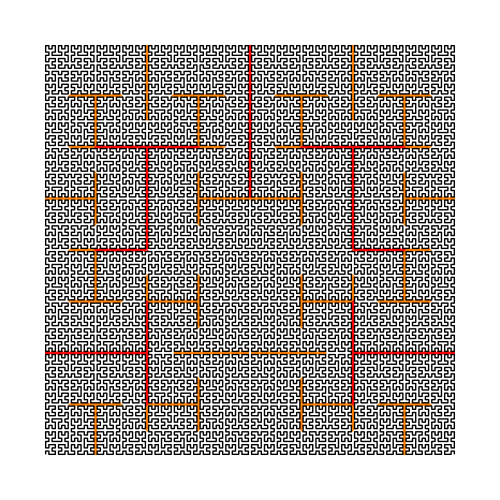

```mathematica
selection=Select[list,#[[2]]-#[[1]]>2^8&&#[[2]]-#[[1]]<=2^10&];
selection2=Select[list,#[[2]]-#[[1]]>2^10&&#[[2]]-#[[1]]<=2^12&];
Rotate[Show[Graphics[{Orange,Line[{data2d[[#[[1]]]],data2d[[#[[2]]]]}]}]&/@selection,Graphics[{Red,Line[{data2d[[#[[1]]]],data2d[[#[[2]]]]}]}]&/@selection2,Graphics[{Thick,HilbertCurve[order]}],ImageSize->500],If[OddQ[order],-Pi/2,0]]
```

```mathematica
Sqrt[8]
```

2 √2